```mathematica
KSetPartitions[Range[5],4]
```

{{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}},{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}},{{1,2},{3},{4},{5}},{{1,3},{2},{4},{5}},{{1,4},{2},{3},{5}},{{1,5},{2},{3},{4}}}

```mathematica
Edges[sets_]:=Select[sets,Length[#]==Length[Flatten[#]]-1&]
```

```mathematica
GraphFromEdges[edges_]:=Block[{h,g,size,current,comp},
size=Length[Flatten[First[edges]]];
h=CompleteGraph[size,VertexLabels->"Name"];
g=h;
Table[
current=First[Select[e,Length[#]==2&]];
g=EdgeDelete[g,UndirectedEdge[current[[1]],current[[2]]]];
,{e,edges}
];
comp=EdgeList[GraphComplement[g]];
{g,Graph[h,GraphLayout->"RadialEmbedding",EdgeLabels->{First[EdgeList[g]]->Style[Framed[Length[edges],Background->White],Red,Bold,14],
EdgeList[g][[2]]->Style[Framed[EdgeCount[h],Background->White],Blue,Bold,14]},
EdgeStyle->Map[#->{Thick,Red}&,comp]]}
]
```

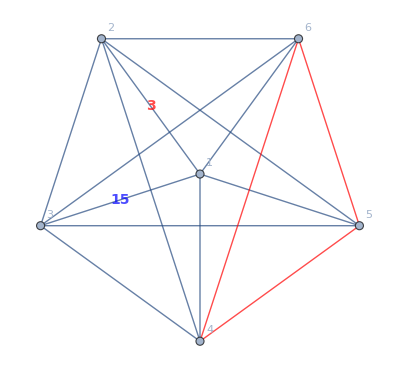
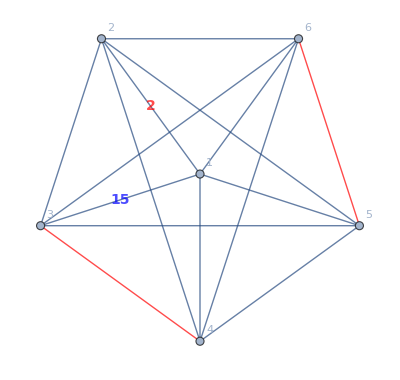
{{-Graphics-,20},{-Graphics-,45}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[6],4]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

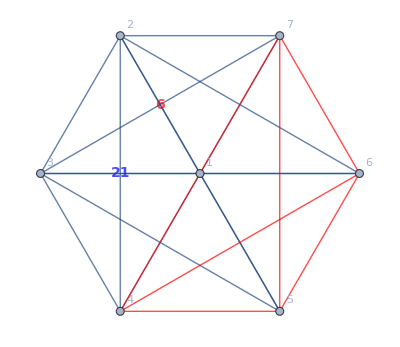
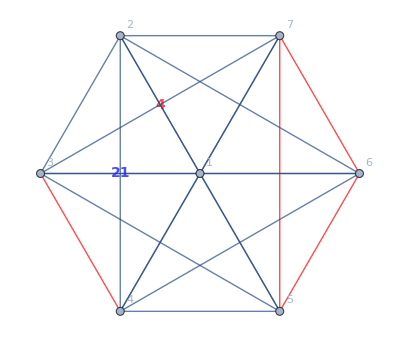
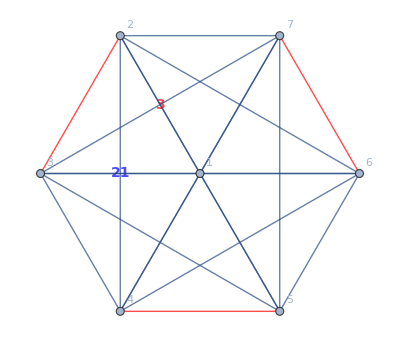
{{-Graphics-,35},{-Graphics-,210},{-Graphics-,105}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Monitor  [Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[7],4]}],set],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

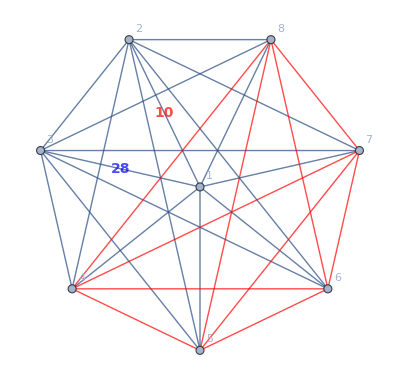
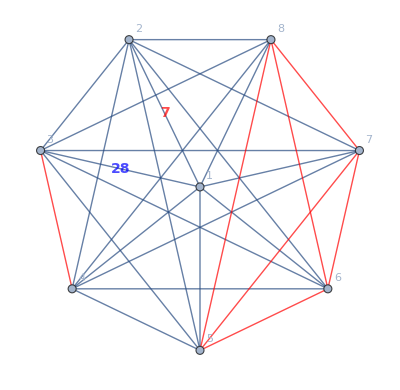
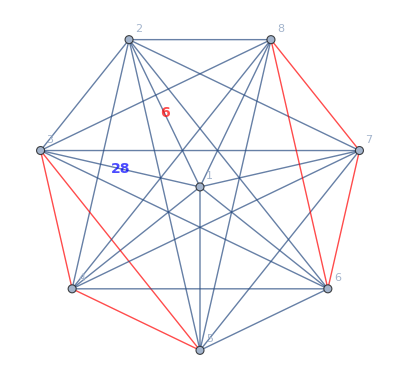
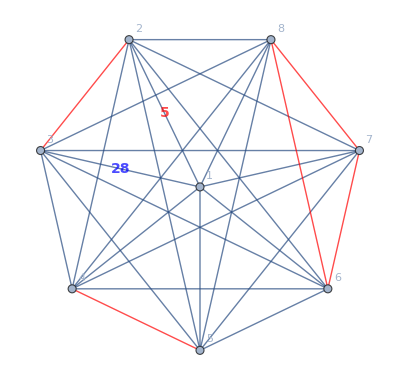
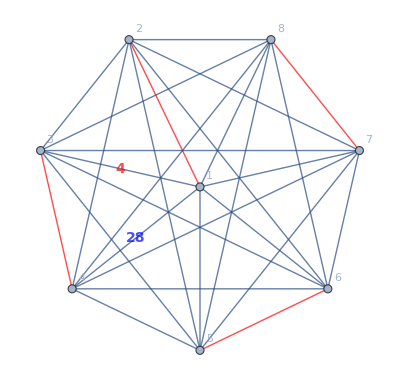
{{-Graphics-,56},{-Graphics-,420},{-Graphics-,280},{-Graphics-,840},{-Graphics-,105}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Monitor  [Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[8],4]}],set],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Monitor  [Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[9],4]}],set],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

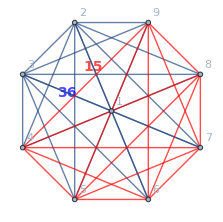
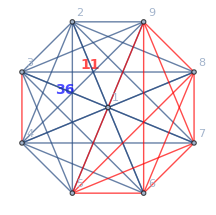
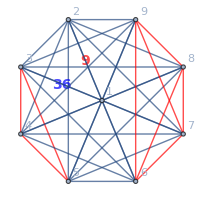
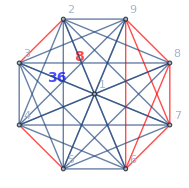
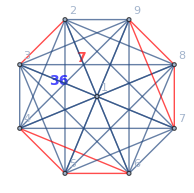
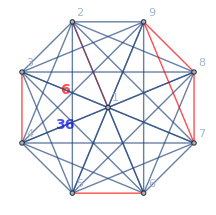
```mathematica
.{{-Graphics-,84},{-Graphics-,756},{-Graphics-,1260},{-Graphics-,1890},{-Graphics-,2520},{-Graphics-,1260}}
```

```mathematica
TableForm[
Table[
Sort[Map[Sort[Map[Length[#]&,#]]&,KSetPartitions[Range[k],4]]//Tally]//Length,
{k,3,13}
], TableDepth->2
]
```

0
1
1
2
3
5
6
9
11
15
18

```mathematica
Table[Count[IntegerPartitions[n],{4,___}],{n,0,60}]
```

{0,0,0,0,1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575}

```mathematica
Table[Length[IntegerPartitions[n,{4}]],{n,0,60}]
```

{0,0,0,0,1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575}

```mathematica
Multicolumn[Table[Style[n,Bold,Darker[Darker[Green]]]->With[{part=IntegerPartitions[n,{4}]},{Style[Length[part],Bold,Blue],part}],{n,0,17}]]
```

0→{0,{}} | 4→{1,{{1,1,1,1}}} | 8→{5,{{5,1,1,1},{4,2,1,1},{3,3,1,1},{3,2,2,1},{2,2,2,2}}} | 12→{15,{{9,1,1,1},{8,2,1,1},{7,3,1,1},{7,2,2,1},{6,4,1,1},{6,3,2,1},{6,2,2,2},{5,5,1,1},{5,4,2,1},{5,3,3,1},{5,3,2,2},{4,4,3,1},{4,4,2,2},{4,3,3,2},{3,3,3,3}}} | 16→{34,{{13,1,1,1},{12,2,1,1},{11,3,1,1},{11,2,2,1},{10,4,1,1},{10,3,2,1},{10,2,2,2},{9,5,1,1},{9,4,2,1},{9,3,3,1},{9,3,2,2},{8,6,1,1},{8,5,2,1},{8,4,3,1},{8,4,2,2},{8,3,3,2},{7,7,1,1},{7,6,2,1},{7,5,3,1},{7,5,2,2},{7,4,4,1},{7,4,3,2},{7,3,3,3},{6,6,3,1},{6,6,2,2},{6,5,4,1},{6,5,3,2},{6,4,4,2},{6,4,3,3},{5,5,5,1},{5,5,4,2},{5,5,3,3},{5,4,4,3},{4,4,4,4}}}
1→{0,{}} | 5→{1,{{2,1,1,1}}} | 9→{6,{{6,1,1,1},{5,2,1,1},{4,3,1,1},{4,2,2,1},{3,3,2,1},{3,2,2,2}}} | 13→{18,{{10,1,1,1},{9,2,1,1},{8,3,1,1},{8,2,2,1},{7,4,1,1},{7,3,2,1},{7,2,2,2},{6,5,1,1},{6,4,2,1},{6,3,3,1},{6,3,2,2},{5,5,2,1},{5,4,3,1},{5,4,2,2},{5,3,3,2},{4,4,4,1},{4,4,3,2},{4,3,3,3}}} | 17→{39,{{14,1,1,1},{13,2,1,1},{12,3,1,1},{12,2,2,1},{11,4,1,1},{11,3,2,1},{11,2,2,2},{10,5,1,1},{10,4,2,1},{10,3,3,1},{10,3,2,2},{9,6,1,1},{9,5,2,1},{9,4,3,1},{9,4,2,2},{9,3,3,2},{8,7,1,1},{8,6,2,1},{8,5,3,1},{8,5,2,2},{8,4,4,1},{8,4,3,2},{8,3,3,3},{7,7,2,1},{7,6,3,1},{7,6,2,2},{7,5,4,1},{7,5,3,2},{7,4,4,2},{7,4,3,3},{6,6,4,1},{6,6,3,2},{6,5,5,1},{6,5,4,2},{6,5,3,3},{6,4,4,3},{5,5,5,2},{5,5,4,3},{5,4,4,4}}}
2→{0,{}} | 6→{2,{{3,1,1,1},{2,2,1,1}}} | 10→{9,{{7,1,1,1},{6,2,1,1},{5,3,1,1},{5,2,2,1},{4,4,1,1},{4,3,2,1},{4,2,2,2},{3,3,3,1},{3,3,2,2}}} | 14→{23,{{11,1,1,1},{10,2,1,1},{9,3,1,1},{9,2,2,1},{8,4,1,1},{8,3,2,1},{8,2,2,2},{7,5,1,1},{7,4,2,1},{7,3,3,1},{7,3,2,2},{6,6,1,1},{6,5,2,1},{6,4,3,1},{6,4,2,2},{6,3,3,2},{5,5,3,1},{5,5,2,2},{5,4,4,1},{5,4,3,2},{5,3,3,3},{4,4,4,2},{4,4,3,3}}} | 
3→{0,{}} | 7→{3,{{4,1,1,1},{3,2,1,1},{2,2,2,1}}} | 11→{11,{{8,1,1,1},{7,2,1,1},{6,3,1,1},{6,2,2,1},{5,4,1,1},{5,3,2,1},{5,2,2,2},{4,4,2,1},{4,3,3,1},{4,3,2,2},{3,3,3,2}}} | 15→{27,{{12,1,1,1},{11,2,1,1},{10,3,1,1},{10,2,2,1},{9,4,1,1},{9,3,2,1},{9,2,2,2},{8,5,1,1},{8,4,2,1},{8,3,3,1},{8,3,2,2},{7,6,1,1},{7,5,2,1},{7,4,3,1},{7,4,2,2},{7,3,3,2},{6,6,2,1},{6,5,3,1},{6,5,2,2},{6,4,4,1},{6,4,3,2},{6,3,3,3},{5,5,4,1},{5,5,3,2},{5,4,4,2},{5,4,3,3},{4,4,4,3}}} |

```mathematica
TriangleNumber[6]
```

21

```mathematica
StirlingS2[10,4]
```

34105

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Monitor  [Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[10],4]}],set],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

```mathematica
Table[Length[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[7],4]}]//Tally//Sort
```

{{3,105},{4,210},{6,35}}

```mathematica
Table[Length[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[6],4]}]//Tally//Sort
```

{{2,45},{3,20}}

```mathematica
Table[Length[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[8],4]}]//Tally//Sort
```

{{4,105},{5,840},{6,280},{7,420},{10,56}}

## Now fro 3

```mathematica
IntegerPartitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

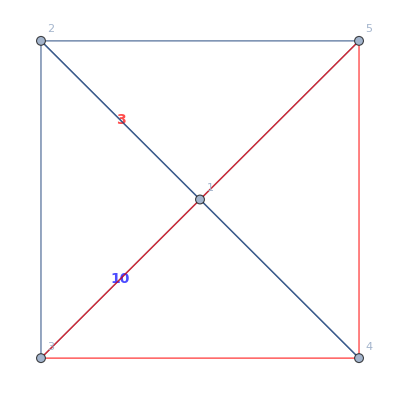
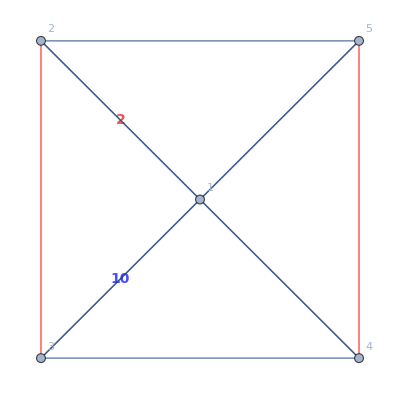
{{-Graphics-,10},{-Graphics-,15}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[5],3]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

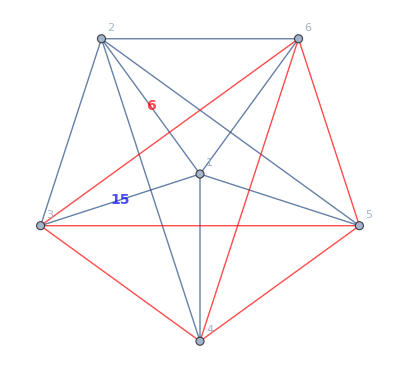
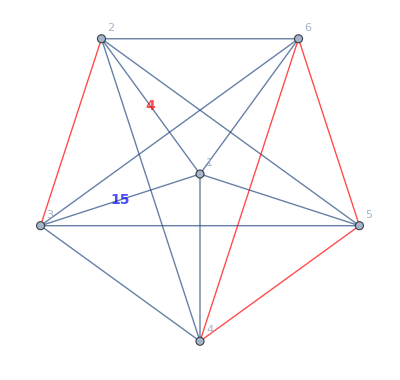
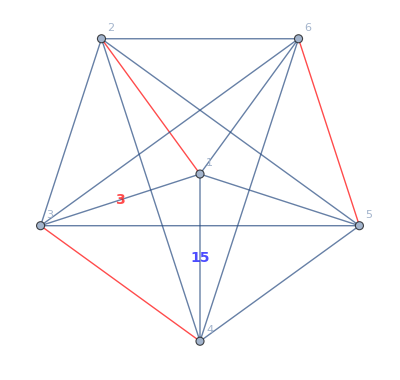
{{-Graphics-,15},{-Graphics-,60},{-Graphics-,15}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[6],3]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

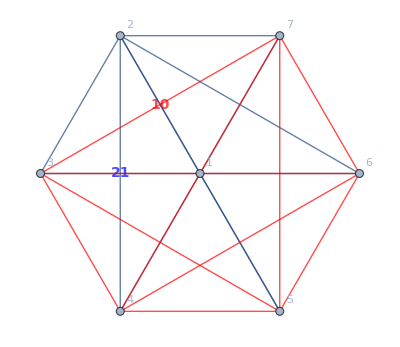
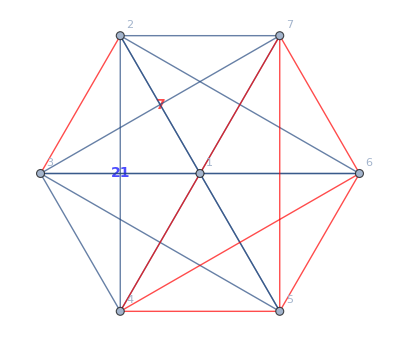
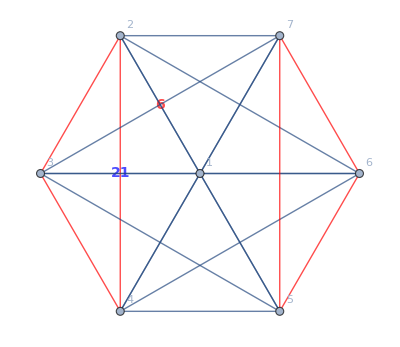
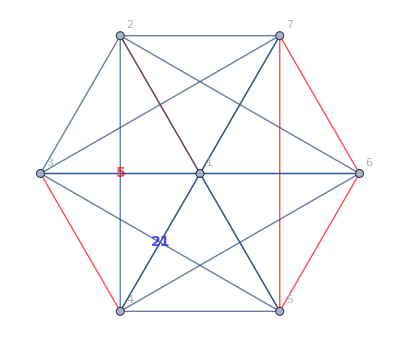
{{-Graphics-,21},{-Graphics-,105},{-Graphics-,70},{-Graphics-,105}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[7],3]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

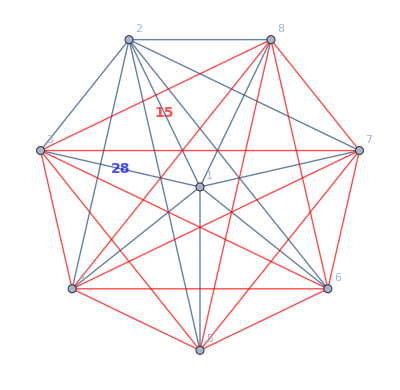
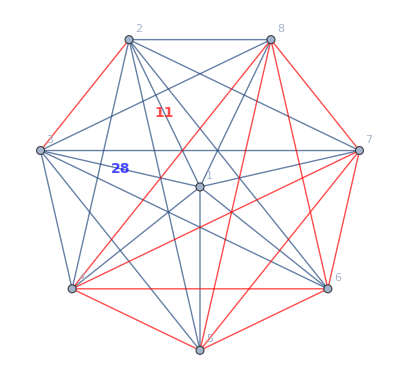
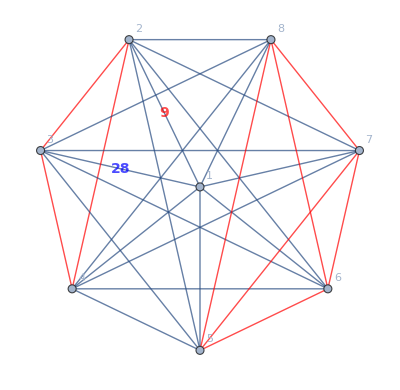
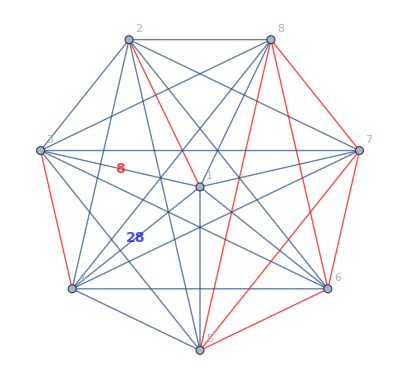
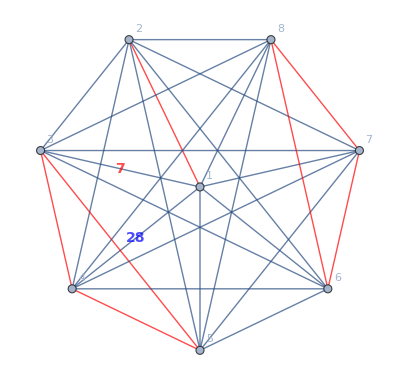
{{-Graphics-,28},{-Graphics-,168},{-Graphics-,280},{-Graphics-,210},{-Graphics-,280}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[8],3]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

## Now fro 2

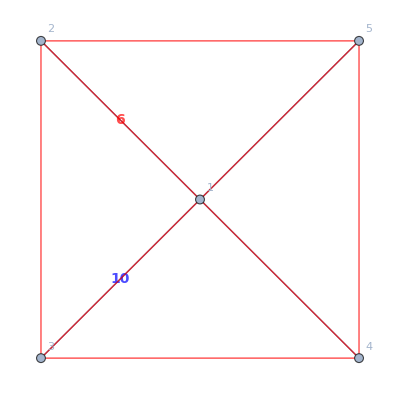
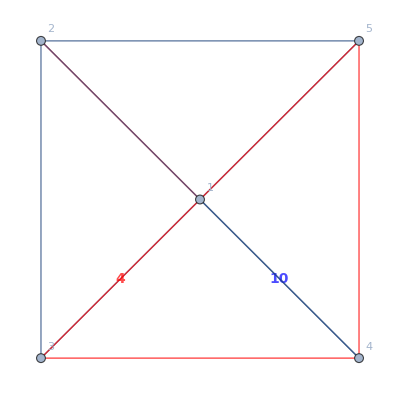
{{-Graphics-,5},{-Graphics-,10}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[5],2]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

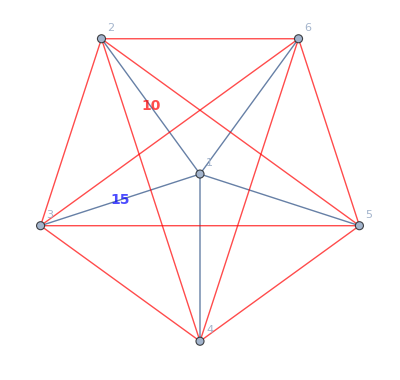
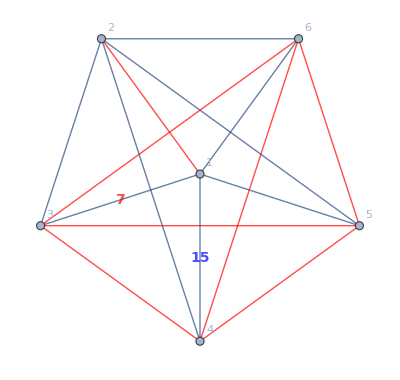
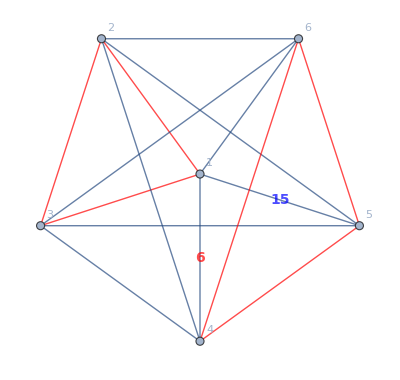
{{-Graphics-,6},{-Graphics-,15},{-Graphics-,10}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[6],2]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

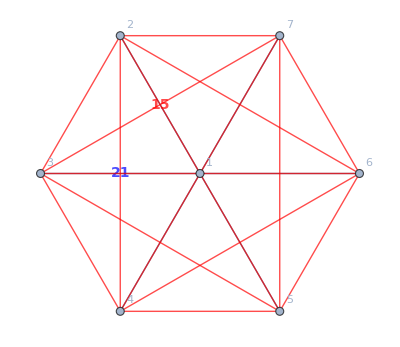
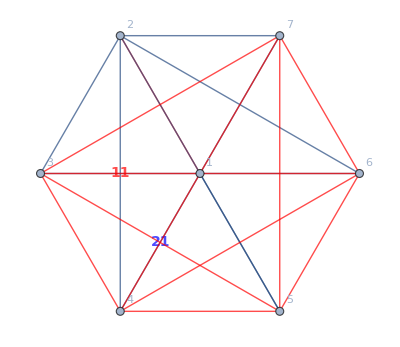
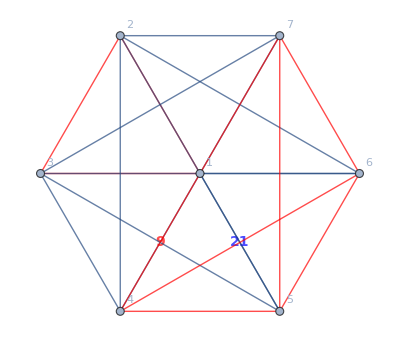
{{-Graphics-,7},{-Graphics-,21},{-Graphics-,35}}

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[7],2]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

```mathematica
Map[{#[[1,2]],#[[2]]}&,Tally[Table[GraphFromEdges[Edges[RecursiveRefinements[set]]],{set,KSetPartitions[Range[8],3]}],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]]
```

{{-Graphics-,28},{-Graphics-,168},{-Graphics-,280},{-Graphics-,210},{-Graphics-,280}}